Renewal/Renewal-Reward/Alternating Processes

Consider a renewal process N(t) in which the life of an element X_i ~ X~ U[0,1], with  μ  =1/2, σ^2 =1/12.  
Then the renewal function  m(t) = E N(t)   satisfies 

                       lim_(t→∞) (m(t) - t/μ)=(σ^2-  μ^2)/(2 μ^2)        ⟹       m(t)≈ t/μ+(σ^2-  μ^2)/(2 μ^2)       for large  t

```mathematica
(1/12-(1/2)^2)/(2(1/2)^2)
```

-1/3

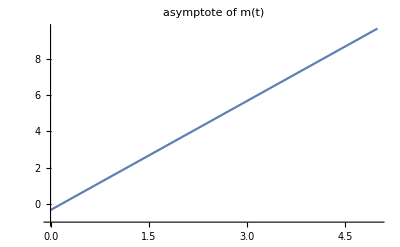

```mathematica
g1=Plot[2t -1/3,{t,0,5},AxesOrigin->{0,-1},PlotLabel->"asymptote of m(t)"]
```

Below  n = 10  samples of  N(t),  N^i(t)  for t ∈ {0, .05, .1, . . . , 5} are simulated 
and the sample average  OverBar[m(t)] =(N^1(t)+...+N^n(t))/n≈m(t) is evaluated

```mathematica
n=10;m̄={}; t=5; dt=.05;p=t/dt;
Do[mt={};   
    Do[Numt={};s=0; s=s+Random[];
     While[s<i*.05,AppendTo[Numt,s];s=s+Random[]];
                  AppendTo[mt,Length[Numt]],
    {n}];
AppendTo[m̄,Mean[mt]],
{i,0,p}]
```

```mathematica
sampleAverage=Table[{i*.05,m̄[[i+1]]},{i,0,100}]//N;
```

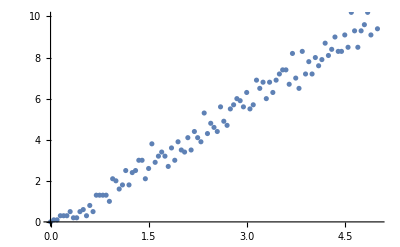

```mathematica
g2=ListPlot[sampleAverage,PlotRange->{{0,5},{0,10}}]
```

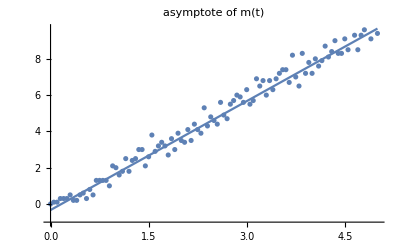

```mathematica
Show[g1,g2]
```

```mathematica
n=1000;t=5; dt=.05;p=t/dt;m̄={};
Do[mt={};   
    Do[Numt={};s=0; s=s+Random[];
     While[s<i*.05,AppendTo[Numt,s];s=s+Random[]];
                  AppendTo[mt,Length[Numt]],
     {n}];
AppendTo[m̄,Mean[mt]],
{i,0,p}]
```

```mathematica
sampleAverage=Table[{i*.05,m̄[[i+1]]},{i,0,100}]//N;
```

```mathematica
g2=ListPlot[sampleAverage,PlotRange->{{0,5},{0,10}}];
```

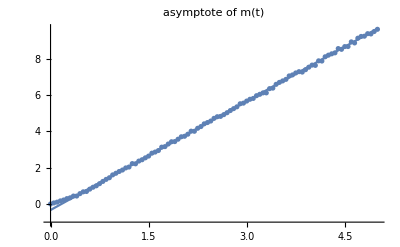

```mathematica
Show[g1,g2]
```

```mathematica
Errors=Table[{i*.05,  m̄[[i+1]]-(2i*.05-1/3)},{i,0,100,10}]//N//TableForm
```

0. | 0.333333
0.5 | 0.00333333
1. | 0.0263333
1.5 | -0.0266667
2. | 0.0373333
2.5 | 0.0533333
3. | 0.00533333
3.5 | 0.0343333
4. | -0.0126667
4.5 | 0.00733333
5. | -0.0396667

Consider a Renewal-Reward Process N(t) with cycle X_n= Y_n+ Z_n, where Y_n~U[0,2] with EY_n=1, 
Z_n~exponential ~λ = 1/2 with EZ_n=1/λ= 2 and reward R_n~U{2,3,...,10} with ER_n= 6.  
Then the reward R_t=∑_(n=1)^(N(t)) R_n for the renewal process corresponding to {X_n} satisfies 

lim_(t→∞) R_t/t=(E [reward in the cycle])/E[time of the cycle]=ER_1/E[Y_1+Z_1]=ER_1/(EY_1+ EZ_1)=2

Below is a simulation of n samples on the interval [0,t]

```mathematica
t=100;Rt={};n=1000;
Do[ TotReward=0;s=0;
   r=Random[Real,{0,2}]+Random[ExponentialDistribution[1/2]];s=s+r;
   While[s<t,TotReward=TotReward+Random[Integer,{2,10}];
              r=Random[Real,{0,2}]+Random[ExponentialDistribution[1/2]];
              s=s+r];
     AppendTo[Rt,TotReward/t],
{n}];
Mean[Rt]//N
```

1.95944

Typical sample

```mathematica
t=100;Rt={};RenewalReward={};TotReward=0;s=0;
r=Random[Real,{0,2}]+Random[ExponentialDistribution[1/2]]; s=s+r; 
      While[s<t,
              Reward=Random[Integer,{2,10}];AppendTo[RenewalReward,{s,Reward}]; 
              TotReward=TotReward+Reward ; 
              r=Random[Real,{0,2}]+Random[ExponentialDistribution[1/2]]; 
              s=s+r];
AppendTo[Rt,TotReward/t];
Mean[Rt]//N
```

2.41

```mathematica
RenewalReward
```

{{2.21487,10},{3.7953,8},{8.43242,6},{10.6004,5},{13.4876,2},{16.9825,8},{17.6942,7},{17.8947,6},{18.4742,2},{20.5257,8},{22.2645,9},{28.6829,2},{31.7403,3},{33.0461,9},{33.2924,8},{38.5026,3},{40.9414,8},{41.967,8},{43.6055,8},{44.4288,9},{51.8416,10},{56.3684,8},{61.6505,10},{66.4497,8},{68.142,3},{70.0569,10},{71.5005,9},{74.3236,9},{78.4463,6},{79.9382,3},{81.8719,9},{84.3647,2},{87.3058,2},{89.3323,7},{93.4565,4},{97.4264,10},{99.5991,2}}

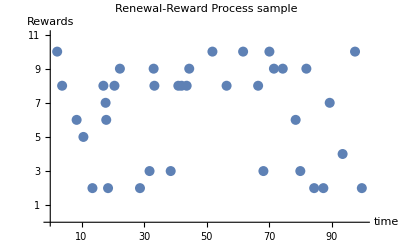

```mathematica
ListPlot[RenewalReward,PlotRange->{{0,100},{0,11}},PlotLabel->"Renewal-Reward Process sample",PlotStyle->PointSize[.018],AxesLabel->{" time","Rewards"},Ticks->{{10,20,30,40,50,60,70,80,90,100},{1,2,3,4,5,6,7,8,9,10,11}}]
```

Consider an Alternating Renewal Process N(t) with  cycle X_n= Y_n+ Z_n, where Z_n~U[1,3] with EZ_n=2, Y_n~exponential ~λ =1/2  with EY_n=1/λ= 2.  Here Z_n="on" = service and Y_n = "off" = waiting time for a customer (which arrives according to Poisson ~λ, and quits whenever the servicing person is busy 
with a customer).  Then the fraction of   "on" time satisfies

lim_(t→∞) E["on" time in [0,t]]/t=(E [on])/E[time of the cycle]=E[on]/E[on +off]=E[on]/(E[on ]+ E[off])=E[Z_1]/(EZ_1+ EY_1)=1/2

Below is a simulation of  n  samples on the interval [0,t]

```mathematica
Z:=Random[Real,{1,3}]; 
Y:=Random[ExponentialDistribution[1/2]];
t=100;n=1000; Ont={};
Do[TotOn=0;
      u=0;on=Z;off=Y;
While[u+on+off<t, u=u+on+off; TotOn=TotOn+on;
         on=Z;off=Y
         ]; 
If[on<t-u, TotOn=TotOn+on,TotOn=TotOn+t-u];AppendTo[Ont,TotOn/t],
{n}];
Mean[Ont]//N
```

0.506544

Typical sample on the interval [0, 20]  that starts with  "on"  at time t = 0.

```mathematica
Z:=Random[Real,{1,3}]; 
Y:=Random[ExponentialDistribution[1/2]];
t=20; OnIntervals={};
Do[u=0;on=Z;  off=Y;
    While[u+on+off<t,
               u=u+on+off;AppendTo[OnIntervals,{u-(on+off),u-off}];
               on=Z;off=Y
              ]; 
     If[on<t-u, AppendTo[OnIntervals,{u,u+on}]],AppendTo[OnIntervals,{u,t}]]
```

```mathematica
OnIntervals
```

{{19.7414,20},{0.,1.10567},{1.47402,3.31365},{3.47682,4.96606},{8.13716,10.8543},{12.5373,13.8185},{14.0872,15.8761},{17.1077,18.83}}

```mathematica
numCycles=Length[OnIntervals]
```

8

To show graphically the "on" - "off" behavior define functions on [0, t] that takes value 1 if "on" and 0 if  "off"

```mathematica
Table[h[k_,s_]:=UnitStep[s-OnIntervals[[k,1]]]-UnitStep[s-OnIntervals[[k,2]]],
                                    {k,1,numCycles}];
```

```mathematica
sample=Table[Plot[h[k,s],{s,0,20},PlotRange->{{0,20},{0,2}},  
                      DisplayFunction->Identity,AxesLabel->{" time","1=on,  0=off "},
                      Ticks->{{20},{1}}],{k,1,numCycles}];
```

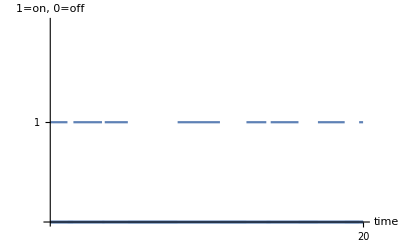

```mathematica
Show[sample,DisplayFunction->$DisplayFunction]
```